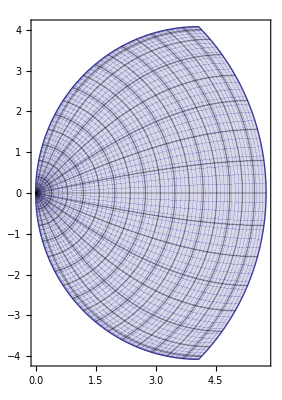

```mathematica
(* Region plot that shows accessible points in sample q-space in transmission experiment. Can also use for glancing experiment if alp is set to very small value. In this case, the lower limit on phi is slightly larger than 0 degree due to the cutoff by the substrate. *)
alp=0 2π/360(*alpha: angle of incidence*);
λ=1.5418 (*wavelength in angstrom*);
thmax=45 2π/360(*Tan[2*th]=Sqrt[X^2+Z^2]/s. The value of thmax is determined primarily by s-distance for a fixed size of CCD screen.*);
qz[th_,phi_]:=4π Sin[th]/λ (Cos[th]Sin[phi]Cos[alp]-Sin[th]Sin[alp]);
qr[th_,phi_]:=Sqrt[(4π Sin[th]/λ)^2-qz[th,phi]^2];
ParametricPlot[{qr[th,phi],qz[th,phi]},{th,0,thmax},{phi,-π/2,π/2}]
```

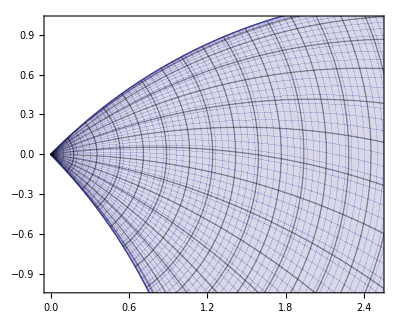

```mathematica
(* Region plot that shows accessible points in sample q-space in transmission experiment. Can also use for glancing experiment if alp is set to very small value. In this case, the lower limit on phi is slightly larger than 0 degree due to the cutoff by the substrate. *)
alp=45 2π/360(*alpha: angle of incidence*);
λ=1.5418 (*wavelength in angstrom*);
thmax=20 2π/360(*Tan[2*th]=Sqrt[X^2+Z^2]/s. The value of thmax is determined primarily by s-distance for a fixed size of CCD screen.*);
qz[th_,phi_]:=4π Sin[th]/λ (Cos[th]Sin[phi]Cos[alp]-Sin[th]Sin[alp]);
qr[th_,phi_]:=Sqrt[(4π Sin[th]/λ)^2-qz[th,phi]^2];
ParametricPlot[{qr[th,phi],qz[th,phi]},{th,0,thmax},{phi,-π/2,π/2},PlotRange->{{0,2.5},{-1,1}}]
```